```mathematica
fin="C:\Users\CCL\Documents\2D_PA_F2_F1_2_1__N51_Len6006_tiles.txt";
```

```mathematica
tiles=Import[fin,"Table","FieldSeparators"->"\t"]
tiles[[All,2]]=ToExpression[tiles[[All,2]]];
tiles[[All,3]]=ToExpression[tiles[[All,3]]];
```

{{{-36.670814840397995, -42.70151346746934},Graphics[Line[{{{-36.670814840397995, -42.70151346746934}, {-36.361797846023045, -43.652569983764494}}, {{-36.670814840397995, -42.70151346746934}, {-37.479831834772945, -42.11372821517687}}, {{-36.670814840397995, -42.70151346746934}, {-36.361797846023045, -41.750456951174186}}, {{-36.361797846023045, -43.652569983764494}, {-36.052780851648095, -42.70151346746934}}, {{-37.479831834772945, -42.11372821517687}, {-37.170814840397995, -41.16267169888172}}, {{-36.361797846023045, -41.750456951174186}, {-36.052780851648095, -42.70151346746934}}, {{-36.361797846023045, -41.750456951174186}, {-37.170814840397995, -41.16267169888172}}}]],{2, 3, 5}},6004,{{28.915289793973585, 42.15929779313991},Graphics[Line[{{{28.9152897939…3973585, 42.5225690571426}}}]],{2, 4}}}
 |  |  |  |

```mathematica
a=2Pi/5;
r1={1,0};
r2={Cos[a],Sin[a]};
r3=Normalize[r1+r2]
basis12 =Graphics[Arrow[{{0,0},#}]&/@{20r1,20r2,30r3},Axes->True];
```

{(1+1/4 (-1+√5))/(√(5/8+(√5)/8+(1+1/4 (-1+√5))^2)),√((5/8+(√5)/8)/(5/8+(√5)/8+(1+1/4 (-1+√5))^2))}

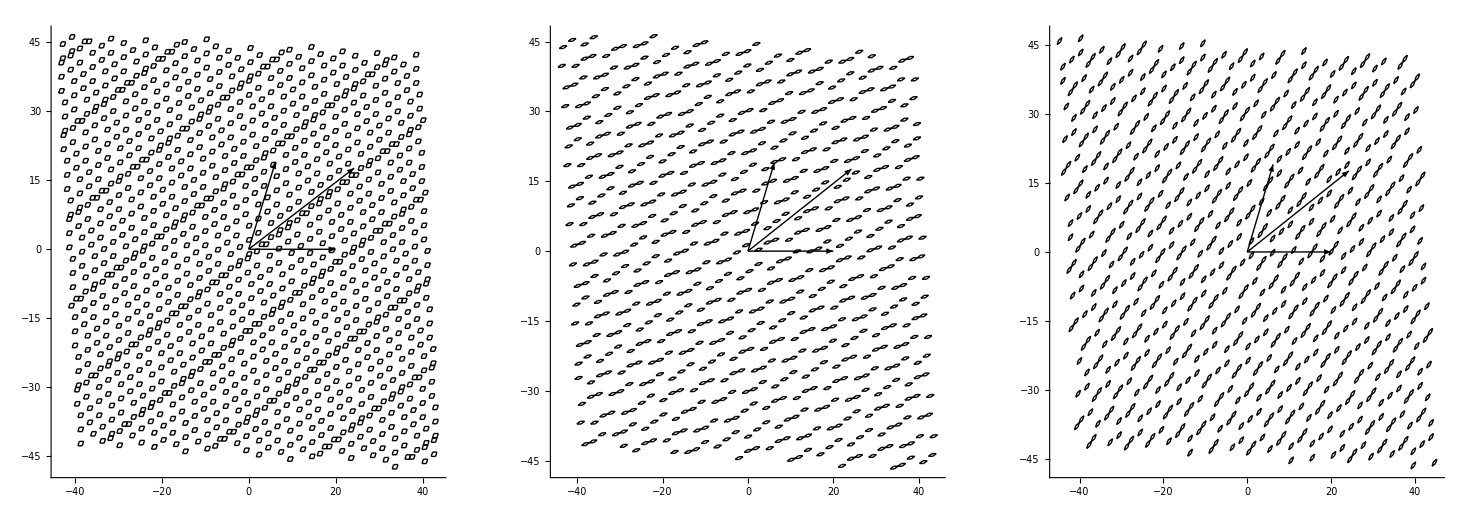

```mathematica
GraphicsRow[
{Show[basis12,tiles[[Flatten[Position[tiles[[All,3]],_?(#=={1,2}&)]],2]],ImageSize->450],
Show[basis12,tiles[[Flatten[Position[tiles[[All,3]],_?(#=={1,4}&)]],2]]],
Show[basis12,tiles[[Flatten[Position[tiles[[All,3]],_?(#=={2,4}&)]],2]]]}
]
```

```mathematica
tiles12=tiles[[Flatten[Position[tiles[[All,3]],_?(#=={1,2}&)]]]];
len=Length[tiles12];
vertices={};
For[i=1,i≤len,i++,vertices=Join[vertices,Flatten[tiles12[[i,2,1,1]],1]];]
tolerance=10^-8;
CountInstances[poslist_,tol_]:=Module[
{curlist,uniqposlist,out,counts,len,uniqlen,counter,curelem,curcompare,i,j},
curlist=poslist;
counts={};
uniqposlist={};
out={};
len=Length[curlist];
For[i=1,i≤len,i++,
curelem=curlist[[i]];
(*-1 indicates already counted*)
If[TrueQ[curelem==-1],
Continue[];,
uniqposlist=Append[uniqposlist,curelem];
];
counter=1;
For[j=i+1,j≤len,j++,
curcompare=curlist[[j]];
If[TrueQ[curcompare==-1],Continue[];];
If[Norm[poslist[[j]]-curelem]<tol,
curlist[[j]]=-1;(*sets to -1 if counted*)
counter=counter+1;
]
];
counts=Append[counts,counter];
];
uniqlen=Length[uniqposlist];
For[i=1,i≤uniqlen,i++,
out=Append[out,{uniqposlist[[i]],counts[[i]]}];
];
out
]
uniquevertices=CountInstances[vertices,tolerance];
```

9528

4500

{{33.0333,-47.7343},2}

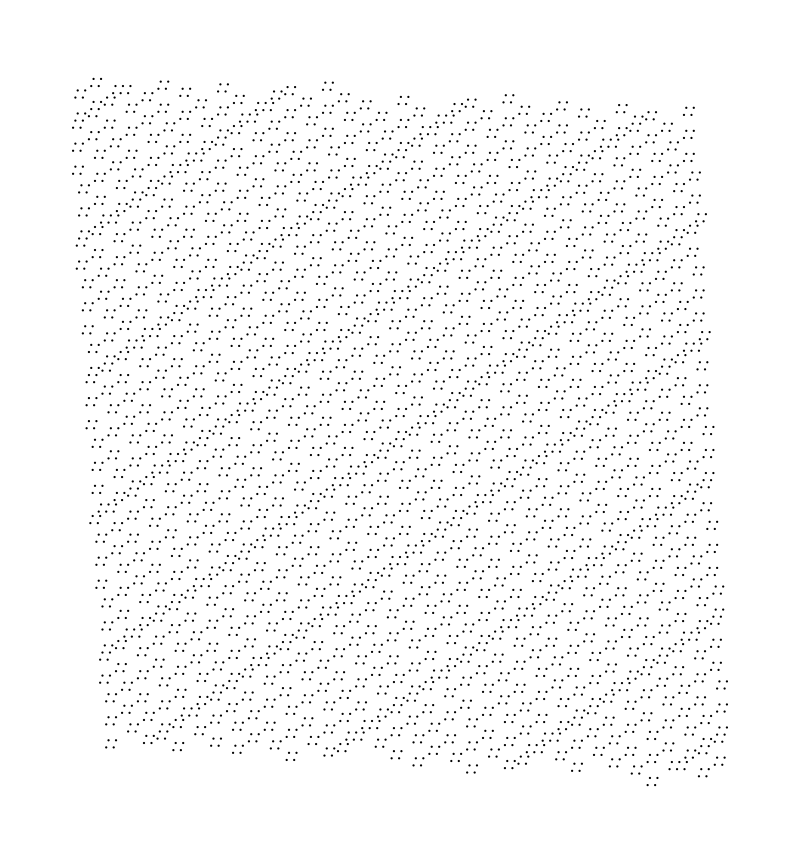

```mathematica
Length[vertices]
Length[uniquevertices]
uniquevertices[[1]]
Graphics[{PointSize[.002],Black,Point[uniquevertices[[All,1]]]},ImageSize->800]
```